# Potential Functions

{Piecewise[{{-1/((1+x^2/y^2) y), y≠0}, {0, True}}],Piecewise[{{x/((1+x^2/y^2) y^2), y≠0}, {0, True}}]}

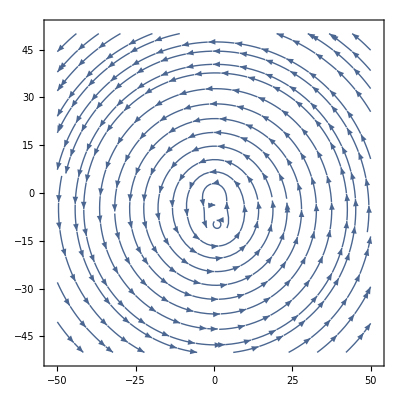

```mathematica
f[x,y] = Piecewise[{{-ArcTan[x/y],y≠ 0}, {0, y == 0}}];
phi[x_,y_] = Grad[f[x,y],{x,y}]
u1[x_,y_] = phi[x,y];
u2[x_,y_] =  phi[x-1,y+10];
U[x_,y_] = u1[x,y] + u2[x,y];
StreamPlot[U[x,y],{x,-50,50},{y,-50,50}]
```

```mathematica
Quit
Remove["Global`*"]
ClearAll
```